## Mathematica dealing with rho from matlab

### Importing cr, cf, and cl1 from Mat bt matlab

```mathematica
rho500dim2=Import["E:\\06_Coh\\00_Code\\00_dim2gs\\00_data\\a0_20191012_rho2_10000.mat"];
CC500dim2=Import["E:\\06_Coh\\00_Code\\00_dim2gs\\00_data\\a0_20191012_cc_10000.mat"];purity500dim2=Import["E:\\06_Coh\\00_Code\\00_dim2gs\\00_data\\a0_20191012_purity_10000.mat"];
rhodim2a=Flatten[rho500dim2,2 ];
(*rhodim2=Flatten[rhodim2a,2];*)

Dimensions[Flatten[rhodim2a,1]];
rho500dim2a=Flatten[rho500dim2,1 ];
Dimensions[rho500dim2a]
Dimensions[rhodim2a];
cl1=Table[2Abs[rho500dim2a[[i]][[1,2]]],{i,10000}];
Dimensions[cl1]

CCdim2a=Flatten[CC500dim2,1];
CCdim2=Flatten[CCdim2a,2];
Dimensions[Flatten[CCdim2,1]];
puritydim2a=Flatten[purity500dim2,1];
puritydim2=Flatten[puritydim2a,2];
Dimensions[Flatten[puritydim2,1]];
Dimensions[CCdim2]
```

{10000,2,2}

{10000}

{10000}

#### Cw versus Cl1

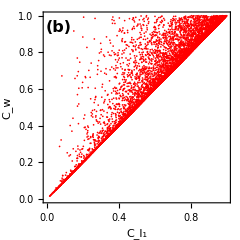

```mathematica
dim =2;
clcrd2=Transpose[{cl1,CCdim2}];
fig001d2b=ListPlot[clcrd2,PlotRange->{{0,1.},{0,1.}},Frame->True,FrameStyle->{{Thick,Thick},{Thick,Thick}},PlotStyle->{{Red,Thick,PointSize[0.005]}},LabelStyle->{15,Bold},FrameLabel->{Style["C_l_1",FontSize->16],Style["C_w",FontSize->16]},FrameTicksStyle->Directive[12.5],Epilog->{Text[Style["(b)",FontSize->16,FontWeight->"Bold"],Scaled[{.08,.92}]](*,Text[Style["dim = 2",FontSize->15,FontWeight->"Bold"],Scaled[{.8,.1}]]*)(*,Text[Style["y = (x+1)/3",FontSize->18,FontWeight->"Bold"],Scaled[{.7,.85}]]*)},ImageSize->{240,240},AspectRatio->1(*,GridLines->{{1/dim},None},GridLinesStyle->Directive[Blue,Dashed]*)]
```

#### Check the ratio of Cw to Cl1

```mathematica
log=0;
For[i=0,i<10000,i++,If[CCdim2[[i]]-cl1[[i]]<0.0000000001,log=log+1,Indeterminate]]
Print[(10000-log)/log]
```

5047/4953

#### CR versus Cl1

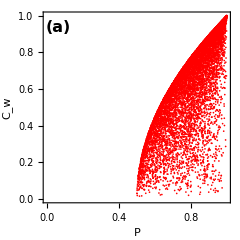

```mathematica
dim =2;
clcrd2=Transpose[{puritydim2,CCdim2}];
fig001d2a=ListPlot[clcrd2,PlotRange->{{0,1.},{0,1.}},Frame->True,FrameStyle->{{Thick,Thick},{Thick,Thick}},PlotStyle->{{Red,Thick,PointSize[0.005]}},LabelStyle->{15,Bold},FrameLabel->{Style["P",FontSize->16],Style["C_w",FontSize->16]},FrameTicksStyle->Directive[12.5],Epilog->{Text[Style["(a)",FontSize->16,FontWeight->"Bold"],Scaled[{.08,.92}]](*,Text[Style["dim = 2",FontSize->15,FontWeight->"Bold"],Scaled[{.2,.1}]]*)(*,Text[Style["y = (x+1)/3",FontSize->18,FontWeight->"Bold"],Scaled[{.7,.85}]]*)},ImageSize->{240,240},AspectRatio->1,GridLines->{{1/dim},None},GridLinesStyle->Directive[Blue,Dashed,Thick]]
```

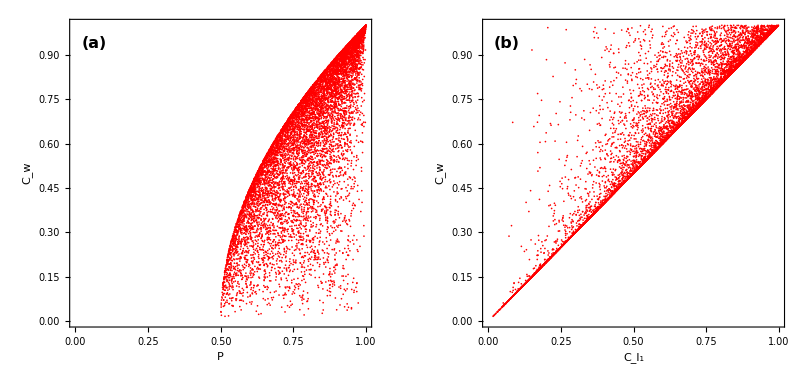

```mathematica
d2=GraphicsGrid[{{fig001d2a,fig001d2b}}]
```

```mathematica
Export["E:\\06_Coh\\00_Code\\01_Plot_qubit\\00_Figures\\00_20191022a_dim2_Cw.eps",d2]
```

E:\06_Coh\00_Code\01_Plot_qubit\00_Figures\00_20191022a_dim2_Cw.eps

### Try

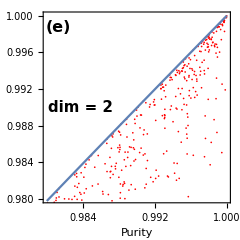

```mathematica
dim =2;
clcrd2=Transpose[{puritydim2,CCdim2}];
fig001d2=ListPlot[clcrd2,PlotRange->{{0.98,1.},{0.98,1.}},Frame->True,FrameStyle->{{Thick,Thick},{Thick,Thick}},PlotStyle->{{Red,Thick,PointSize[0.005]}},LabelStyle->{15,Bold},FrameLabel->{Style["Purity",FontSize->16],Style["C̄",FontSize->16]},FrameTicksStyle->Directive[12.5],Epilog->{Text[Style["(e)",FontSize->16,FontWeight->"Bold"],Scaled[{.08,.92}]],Text[Style["dim = 2",FontSize->15,FontWeight->"Bold"],Scaled[{.2,.5}]](*,Text[Style["y = (x+1)/3",FontSize->18,FontWeight->"Bold"],Scaled[{.7,.85}]]*)},ImageSize->{240,240},AspectRatio->1,GridLines->{{1/dim},None},GridLinesStyle->Directive[Blue,Dashed]];
fig002d2=Plot[(2x-1)^(1/2),{x,0.98,1}];
Show[fig001d2,fig002d2]
(*fig002d3=Plot[{x},{x,0,1.05},PlotRange->{{0,1.05},{0,1.05}},PlotStyle->{{Thickness[0.005],Darker[Green],Dashed}}];(* d1 is dim *)
figdim3=Show[fig001d3,fig002d3]*)
```

```mathematica
Dimensions[rho500dim2];
rho1=rho500dim2[[1,1]];
2Abs[rho1[[1,2]]]
CCdim2[[1]]
puritydim2[[1]];
```

0.391902

0.391902

```mathematica
Dimensions[rho500dim2];
rho2=rho500dim2[[1,2]];
2Abs[rho2[[1,2]]]
CCdim2[[2]]
puritydim2[[2]];
```

0.427944

0.427944

```mathematica
Dimensions[rho500dim2]
rho1000=rho500dim2[[1,1000]]
CCdim2[[1000]]
puritydim2[[1000]]
```

{1,10000,2,2}

{{0.43658+0. ⅈ,0.455549-0.120206 ⅈ},{0.455549+0.120206 ⅈ,0.56342+0. ⅈ}}

0.94502

0.951994

```mathematica
rho1000=rho500dim2[[1,1000]]
Inverse[rho1000]
```

{{0.43658+0. ⅈ,0.455549-0.120206 ⅈ},{0.455549+0.120206 ⅈ,0.56342+0. ⅈ}}

{{23.4727-2.47051×10^-15 ⅈ,-18.9787+5.00793 ⅈ},{-18.9787-5.00793 ⅈ,18.1884-2.87332×10^-15 ⅈ}}

```mathematica
1-1/18.1884//N
```

0.94502

```mathematica
2Abs[rho1000[[1,2]]]
```

0.942284